```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\GitHub\collab-optimizer\data

```mathematica
ClearAll[dat]
```

```mathematica
AvgSimRunDat[θ_,τ_]:=Module[{sdat},
Mean[(sdat=<<("microsim-theta_"<>θ<>"-tau_"<>τ<>"-run_"<>ToString[#]<>".txt");
Length@Cases[SplitBy[sdat,Last],Except[{___,{_,0},___}]])&/@Range[1,100]]/30
]
```

```mathematica
processSimDat=Table[{ToExpression[τ],AvgSimRunDat[θ,τ]},{θ,{"0.1","1.0","10.0"}},{τ,{"2","3","4","5","6"}}]
```

{{{2,1159/120},{3,1197/125},{4,2369/250},{5,2807/300},{6,9211/1000}},{{2,10},{3,10},{4,10},{5,2977/300},{6,9221/1000}},{{2,10},{3,10},{4,10},{5,10},{6,6911/750}}}

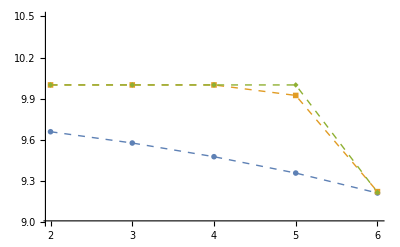

```mathematica
ListPlot[processSimDat,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick,Dashed],PlotRange->{Automatic,{9,10.5}}]
```

```mathematica
Length[Select[SplitBy[dat[6,.1],Last[#]≥4&],MemberQ[Last[Transpose[#]],x_/;x≥ 4]&]]
```

236

```mathematica
AvgRealRunDat[θ_,τ_]:=Module[{dat},
dat[θ,τ]=<<("task_alloc_"<>τ<>"_"<>θ<>".txt");
Length[Select[SplitBy[dat[θ,τ],Last[#]≥4&],MemberQ[Last[Transpose[#]],x_/;x≥ 4]&]]/30]
```

```mathematica
processRealDat=Table[{ToExpression[τ],AvgRealRunDat[θ,τ]},{θ,{"0.1","1.0","10.0"}},{τ,{"2","3","4","5","6"}}]
```

{{{2,139/15},{3,79/10},{4,87/10},{5,259/30},{6,118/15}},{{2,271/30},{3,73/10},{4,76/15},{5,74/15},{6,149/30}},{{2,23/5},{3,37/6},{4,38/5},{5,21/5},{6,21/10}}}

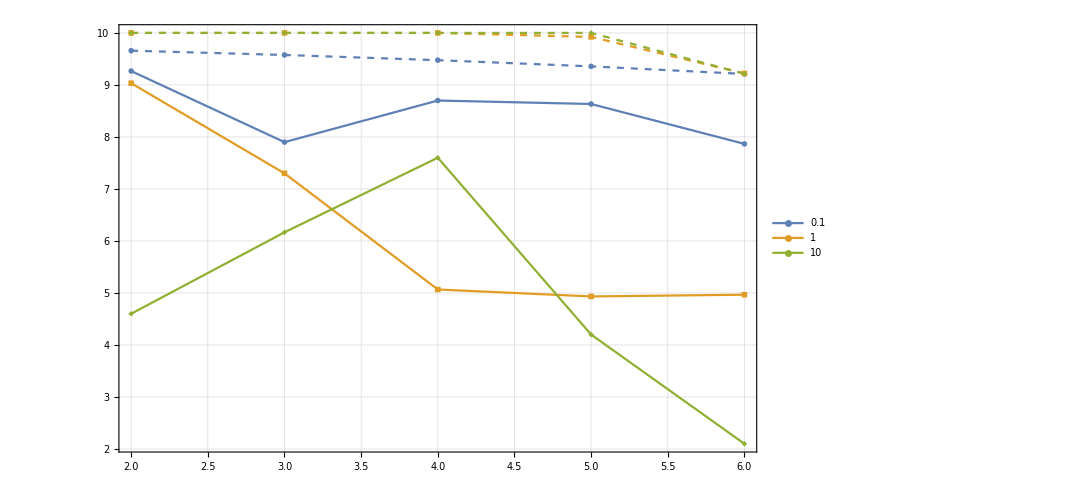

```mathematica
Show[ListPlot[processRealDat,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick],PlotTheme->"Detailed",ImageSize->800,PlotLegends->{0.1,1,10},PlotRange->{Automatic,{11,2}}],ListPlot[processSimDat,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick,Dashed]]]
```